```mathematica
δ[p_,q_,k1_]:=Subscript[δ, 0]+(Subscript[δ, 1]-Subscript[δ, 0])*Exp[-(p-q)^2/(2*k1^2)];
ρ[p_,k2_]:=Subscript[ρ, 0]+(Subscript[ρ, 1]-Subscript[ρ, 0])*Exp[-p^2/(2*k2^2)];
μ[q_,k3_]:=Subscript[μ, 0]+(Subscript[μ, 1]-Subscript[μ, 0])Exp[-q^2/(2*k3^2)];
```

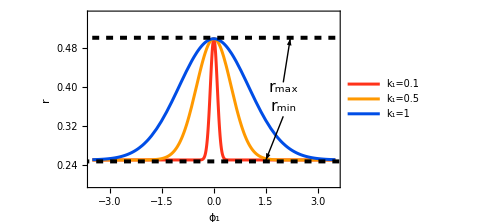

```mathematica
Subscript[ρ, 0]=0.25;Subscript[ρ, 1]=0.5;
i=Plot[{ρ[p,0.1],ρ[p,0.5], ρ[p,1]},{p,-3.5,3.5},PlotRange->{{-3.5,3.5},{0.2,0.55}},PlotStyle->{{RGBColor[1.0,0.2,0.1],Thickness[0.006]},(*Fiery Red-Orange*){RGBColor[1.0,0.6,0.0],Thickness[0.006]},(*Golden Orange*){RGBColor[0.0,0.3,0.9],Thickness[0.006]}    (*Deep Blue Contrast*)},PlotLegends->Placed[LineLegend[{"k_1=0.1","k_1=0.5","k_1=1"},LegendFunction->(Framed[#,Background->White,FrameStyle->Black]&),LegendLayout->"Column"],{0.15,0.75}],Axes->False,Frame->True,FrameLabel->{"ϕ_1","r"},LabelStyle->{FontSize->16},FrameStyle->Directive[Black,Thickness[0.003]],Epilog->{Inset[Style["r_max",16,Black],{2,0.4}],Inset[Style["r_min",16,Black],{2,0.36}]},ImageSize->Medium];
j=ContourPlot[{{ρ==0.247},{ρ==0.502}},{p,-7.5,7.5},{ρ,0.2,0.55},ContourStyle->{{Black,Dashed,Thickness[0.008]}}];
j1=Graphics[{Arrow[{{2,0.41},{2.2,.5}}],Arrow[{{2,0.87},{2,0.77}}]}];
j2=Graphics[{Arrow[{{2,0.34},{1.5,0.25}}],Arrow[{{2,0.87},{2,0.77}}]}];
s1=Show[i,j,j1,j2]
```

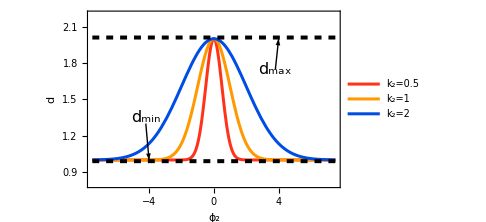

```mathematica
Subscript[μ, 0]=1;Subscript[μ, 1]=2;
i=Plot[{μ[p,0.5],μ[p,1], μ[p,2]},{p,-7.5,7.5},PlotRange->{{-7.5,7.5},{0.8,2.2}},PlotStyle->{{RGBColor[1.0,0.2,0.1],Thickness[0.006]},(*Fiery Red-Orange*){RGBColor[1.0,0.6,0.0],Thickness[0.006]},(*Golden Orange*){RGBColor[0.0,0.3,0.9],Thickness[0.006]}    (*Deep Blue Contrast*)},PlotLegends->Placed[LineLegend[{"k_2=0.5","k_2=1","k_2=2"},LegendFunction->(Framed[#,Background->White,FrameStyle->Black]&),LegendLayout->"Column"],{0.13,0.75}],Axes->False,Frame->True,FrameLabel->{"ϕ_2","d"},LabelStyle->{FontSize->16},FrameStyle->Directive[Black,Thickness[0.003]],Epilog->{Inset[Style["d_max",16,Black],{3.8,1.75}],Inset[Style["d_min",16,Black],{-4.2,1.35}]},ImageSize->Medium];
j=ContourPlot[{{μ==2.01},{μ==0.99}},{p,-7.5,7.5},{μ,0.9,2.1},ContourStyle->{{Black,Dashed,Thickness[0.008]}}];
j1=Graphics[{Arrow[{{-4.2,1.3},{-4,1}}]}];
j2=Graphics[{Arrow[{{3.8,1.75},{4,2}}]}];
s2=Show[i,j,j1,j2]
```

```mathematica
Subscript[δ, 0]=1;Subscript[δ, 1]=2;
s3=Plot3D[δ[p,q,0.1],{p,-1,1},{q,-1,1},Boxed->True,BoxStyle->Directive[Black,Thickness[0.003]],ColorFunction->"BrightBands",PlotLegends->None,AxesLabel->{Subscript[ϕ, 1],Subscript[ϕ, 2],g},LabelStyle->{FontSize->16,Black},ImageSize->250,ViewPoint->{1.5,1,0.7}]
s4=Plot3D[δ[p,q,0.5],{p,-3,3},{q,-3,3},Boxed->True,BoxStyle->Directive[Black,Thickness[0.003]],ColorFunction->"BrightBands",PlotLegends->None,AxesLabel->{Subscript[ϕ, 1],Subscript[ϕ, 2],g},LabelStyle->{FontSize->16,Black},ImageSize->250,ViewPoint->{1.5,1,0.7}]
s5=Plot3D[δ[p,q,1],{p,-3,3},{q,-3,3},Boxed->True,BoxStyle->Directive[Black,Thickness[0.003]],ColorFunction->"BrightBands",PlotLegends->BarLegend[{"BrightBands",{1,2}}],AxesLabel->{Subscript[ϕ, 1],Subscript[ϕ, 2],g},LabelStyle->{FontSize->16,Black},ImageSize->250,ViewPoint->{1.5,1,0.7}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
g1=Grid[{{Style["A",20],Style["B",20]},{s1,s2}},Alignment->Center,Spacings->{-0.1,- 0.65}]
g2=Grid[{{Style["C: k_3=0.1",20],Style["D: k_3=0.5",20],Style["E: k_3=1",20]},{s3,s4,s5}},Alignment->Center,Spacings->{-0.7,- 0.3}]
```

A | B
-Graphics- | -Graphics-

C: k_3=0.1 | D: k_3=0.5 | E: k_3=1
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
g=Grid[{{g1},{g2}},Alignment->Center]
```

A | B
-Graphics- | -Graphics-
C: k_3=0.1 | D: k_3=0.5 | E: k_3=1
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Export[SystemDialogInput["FileSave","normal.pdf"],g,ImageResolution->350,"CompressionLevel"->0]
```

C:\Users\SANTANA\Dropbox\SANTANA\P7_G function\Mondal_allee effect\normal.pdf

```mathematica
δ[p_,q_]:=Subscript[δ, 0]+(Subscript[δ, 1]-Subscript[δ, 0])*Exp[-(p-q)^2/(2*k1^2)];
ρ[p_]:=Subscript[ρ, 0]+(Subscript[ρ, 1]-Subscript[ρ, 0])*Exp[-p^2/(2*k2^2)];
μ[q_]:=Subscript[μ, 0]+(Subscript[μ, 1]-Subscript[μ, 0])Exp[-q^2/(2*k3^2)];
```

```mathematica
ρ'[p]/ρ[p]==-μ'[q]/μ[q]
```

-(ⅇ^(-p^2/(2 k2^2)) p (-ρ_0+ρ_1))/(k2^2 (ρ_0+ⅇ^(-p^2/(2 k2^2)) (-ρ_0+ρ_1)))==(ⅇ^(-q^2/(2 k3^2)) q (-μ_0+μ_1))/(k3^2 (μ_0+ⅇ^(-q^2/(2 k3^2)) (-μ_0+μ_1)))

```mathematica
D[δ[p,q],{p,1}]
D[δ[p,q],{q,1}]
D[δ[p,q],{p,1}]+D[δ[p,q],{q,1}]
```

-(ⅇ^(-(p-q)^2/(2 k1^2)) (p-q) (-δ_0+δ_1))/k1^2

(ⅇ^(-(p-q)^2/(2 k1^2)) (p-q) (-δ_0+δ_1))/k1^2

0

```mathematica
D[δ[p,q],{p,2}]
D[δ[p,q],{q,2}]
D[δ[p,q],{p,2}]-D[δ[p,q],{q,2}]
```

(-(ⅇ^(-(p-q)^2/(2 k1^2)))/k1^2+(ⅇ^(-(p-q)^2/(2 k1^2)) (p-q)^2)/k1^4) (-δ_0+δ_1)

(-(ⅇ^(-(p-q)^2/(2 k1^2)))/k1^2+(ⅇ^(-(p-q)^2/(2 k1^2)) (p-q)^2)/k1^4) (-δ_0+δ_1)

0

```mathematica
ρ'[p]
ρ''[p]
```

-(ⅇ^(-p^2/(2 k2^2)) p (-ρ_0+ρ_1))/k2^2

-(ⅇ^(-p^2/(2 k2^2)) (-ρ_0+ρ_1))/k2^2+(ⅇ^(-p^2/(2 k2^2)) p^2 (-ρ_0+ρ_1))/k2^4

```mathematica
μ'[q]
μ''[q]
```

-(ⅇ^(-q^2/(2 k3^2)) q (-μ_0+μ_1))/k3^2

-(ⅇ^(-q^2/(2 k3^2)) (-μ_0+μ_1))/k3^2+(ⅇ^(-q^2/(2 k3^2)) q^2 (-μ_0+μ_1))/k3^4